```mathematica
ClearAll["Global`*"]
```

```mathematica
r=√(x^2+y^2+z^2);
X={x,y,z};
Γ={{0,1,0},{0,0,0},{0,0,0}};
Γ'=Transpose[Γ];
XX=Outer[Times,X,X]
```

{{x^2,x y,x z},{x y,y^2,y z},{x z,y z,z^2}}

```mathematica
Γdoubledot=Total[Total[Table[Γ[[i]]  XX[[i]],{i,1,3}]]];
Γ1=Total[Total[Table[Γ[[i]]  Γ'[[i]],{i,1,3}]]];
Γ2=Total[Total[Table[Γ[[i]]  Γ[[i]],{i,1,3}]]];
Γ3=Total[Total[Table[Γ'[[i]]  Γ[[i]],{i,1,3}]]];
Γ4=Total[Total[Table[Γ'[[i]]  Γ'[[i]],{i,1,3}]]];
(*Define the parameter λ*)ClearAll[λ]
```

```mathematica
c1=5005/1144;
c2=5;
c3=19305/10296;
c4=25/4;
c5=5/2;
c6=42042/41184;
c7=1/2;
c8=35178/41184;
c9=426426/144144;
c10=1;
c11=234234/144144;
c12=4911/10092;
c13=2399/10092;
c14=1/4;
c15=1/6;
c17=179179/480480;
c18=171171/480480;
```

```mathematica
p=((-(5 c14)/(2 r^12)+c2/r^10-(7 c3)/(4 r^9)+(3 c4)/(4 r^8)-(5 c7)/r^7+c5/(2 r^5))Γdoubledot^2 +(-c14/(2 r^10)+c3/(2 r^7)-c4/(4 r^6)-c15/r^5-c5/(6 r^3))(Γ.X).(Γ.X)+(-c14/r^10+c3/r^7-c4/(2 r^6)+c7/r^5)(Γ.X).(Γ'.X)+(-c14/(2 r^10)+c3/(2 r^7)-c4/(4 r^6)+(2 c10)/r^5+c5/(6 r^3))(Γ'.X).(Γ'.X)+(-c3/(10 r^5)+c4/(12 r^4)-c5/(6 r))(Γ1+Γ2))
```

-3/(16 (x^2+y^2+z^2)^(5/2))+25/(48 (x^2+y^2+z^2)^2)-5/(12 √(x^2+y^2+z^2))+x^2 y^2 (-5/(8 (x^2+y^2+z^2)^6)+5/((x^2+y^2+z^2)^5)-105/(32 (x^2+y^2+z^2)^(9/2))+75/(16 (x^2+y^2+z^2)^4)-5/(2 (x^2+y^2+z^2)^(7/2))+5/(4 (x^2+y^2+z^2)^(5/2)))+y^2 (-1/(8 (x^2+y^2+z^2)^5)+15/(16 (x^2+y^2+z^2)^(7/2))-25/(16 (x^2+y^2+z^2)^3)-1/(6 (x^2+y^2+z^2)^(5/2))-5/(12 (x^2+y^2+z^2)^(3/2)))+x^2 (-1/(8 (x^2+y^2+z^2)^5)+15/(16 (x^2+y^2+z^2)^(7/2))-25/(16 (x^2+y^2+z^2)^3)+2/((x^2+y^2+z^2)^(5/2))+5/(12 (x^2+y^2+z^2)^(3/2)))

```mathematica
p1=p/.z->0;
p2=p/.y->0;
p3=p/.x->0;
```

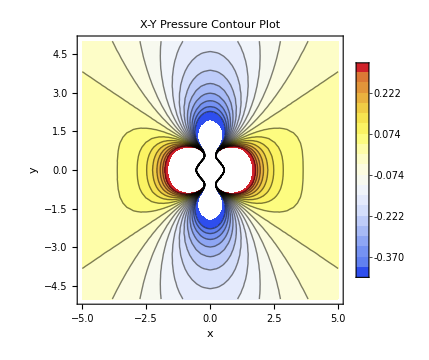

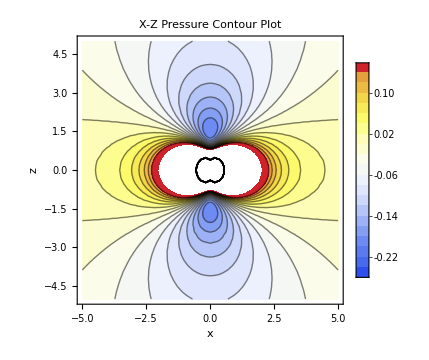

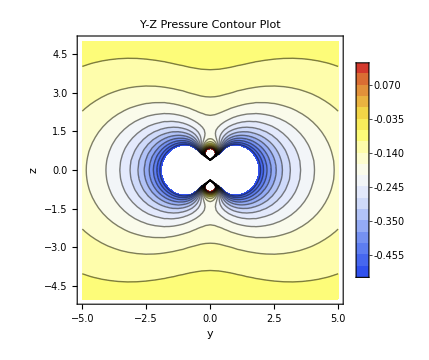

```mathematica
S1=ContourPlot[p1,{x,-5,5},{y,-5,5},Contours->20,ContourShading->True,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,Frame->True,FrameLabel->{"x","y"},Axes->False,PlotLabel->Style["X-Y Pressure Contour Plot",14,Bold],ImageSize->Medium,PlotLegends->Automatic]
S2=ContourPlot[p2,{x,-5,5},{z,-5,5},Contours->20,ContourShading->True,ColorFunction->"TemperatureMap",(*Smooth,perceptual color scale*)ColorFunctionScaling->True,Frame->True,FrameLabel->{"x","z"},Axes->False,PlotLabel->Style["X-Z Pressure Contour Plot",14,Bold],ImageSize->Medium,PlotLegends->Automatic]
S3=ContourPlot[p3,{y,-5,5},{z,-5,5},Contours->20,ContourShading->True,ColorFunction->"TemperatureMap",(*Smooth,perceptual color scale*)ColorFunctionScaling->True,Frame->True,FrameLabel->{"y","z"},Axes->False,PlotLabel->Style["Y-Z Pressure Contour Plot",14,Bold],ImageSize->Medium,PlotLegends->Automatic]
```

```mathematica
psphEvaluated=p/.{x->r Sin[θ]Cos[ϕ],y->r Sin[θ]Sin[ϕ],z->r Cos[θ],Assumptions-> {Im[r]==0,Re[r]>0}}/.(x^2+y^2+z^2)->1
```

-3/(16 (Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(5/2))+25/(48 (Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^2)-5/(12 √(Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2))+Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2 (-5/(8 (Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^6)+5/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^5)-105/(32 (Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(9/2))+75/(16 (Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^4)-5/(2 (Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(7/2))+5/(4 (Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(5/2)))+Sin[θ]^2 Sin[ϕ]^2 (-1/(8 (Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^5)+15/(16 (Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(7/2))-25/(16 (Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^3)-1/(6 (Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(5/2))-5/(12 (Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(3/2)))+Cos[ϕ]^2 Sin[θ]^2 (-1/(8 (Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^5)+15/(16 (Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(7/2))-25/(16 (Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^3)+2/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(5/2))+5/(12 (Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(3/2)))

```mathematica
pcode=(-1/(8 r^10)-55/(72 r^7)-25/(16 r^6)-1003/(800 r^5)+5/(12 r^3)) (Γ'.X).(Γ'.X)+(-1/(8 r^10)-55/(72 r^7)-25/(16 r^6)-1003/(800 r^5)+5/(12 r^3))(Γ.X).(Γ'.X)+(-1/(8 r^10)-55/(72 r^7)-25/(16 r^6)-1027/(800 r^5)-5/(12 r^3)) (Γ'.X).(Γ.X)+(-1/(8 r^10)-55/(72 r^7)-25/(16 r^6)-1027/(800 r^5)-5/(12 r^3)) (Γ.X).(Γ.X)+20/576 (-18/r^12+144/r^10+154/r^9+135/r^8-72/r^7+36/r^5) Γdoubledot^2+1/720 (220/r^5+750/r^4+1458/r^3+2625/r-120 r^2)((Γ1+Γ2+Γ3+Γ4)/4)+1/12 (-7/r-2 r^2) ((-Γ1+Γ2-Γ3+Γ4)/4)
```

5/144 x^2 y^2 (-18/((x^2+y^2+z^2)^6)+144/((x^2+y^2+z^2)^5)+154/((x^2+y^2+z^2)^(9/2))+135/((x^2+y^2+z^2)^4)-72/((x^2+y^2+z^2)^(7/2))+36/((x^2+y^2+z^2)^(5/2)))+y^2 (-1/(8 (x^2+y^2+z^2)^5)-55/(72 (x^2+y^2+z^2)^(7/2))-25/(16 (x^2+y^2+z^2)^3)-1027/(800 (x^2+y^2+z^2)^(5/2))-5/(12 (x^2+y^2+z^2)^(3/2)))+x^2 (-1/(8 (x^2+y^2+z^2)^5)-55/(72 (x^2+y^2+z^2)^(7/2))-25/(16 (x^2+y^2+z^2)^3)-1003/(800 (x^2+y^2+z^2)^(5/2))+5/(12 (x^2+y^2+z^2)^(3/2)))+(220/((x^2+y^2+z^2)^(5/2))+750/((x^2+y^2+z^2)^2)+1458/((x^2+y^2+z^2)^(3/2))+2625/(√(x^2+y^2+z^2))-120 (x^2+y^2+z^2))/1440+1/24 (-7/(√(x^2+y^2+z^2))-2 (x^2+y^2+z^2))

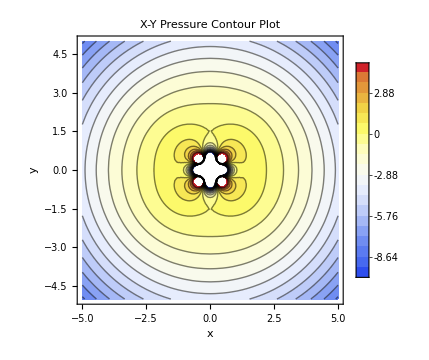

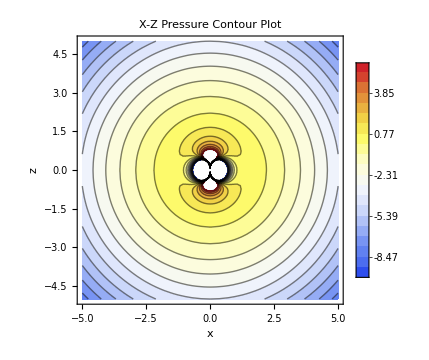

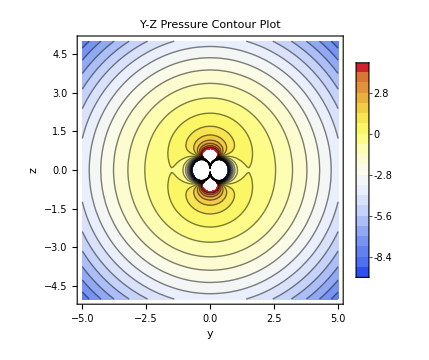

```mathematica
pcode1=pcode/.z->0;
pcode2=pcode/.y->0;
pcode3=pcode/.x->0;
Scode1=ContourPlot[pcode1,{x,-5,5},{y,-5,5},Contours->20,ContourShading->True,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,Frame->True,FrameLabel->{"x","y"},Axes->False,PlotLabel->Style["X-Y Pressure Contour Plot",14,Bold],ImageSize->Medium,PlotLegends->Automatic]
Scode2=ContourPlot[pcode2,{x,-5,5},{z,-5,5},Contours->20,ContourShading->True,ColorFunction->"TemperatureMap",(*Smooth,perceptual color scale*)ColorFunctionScaling->True,Frame->True,FrameLabel->{"x","z"},Axes->False,PlotLabel->Style["X-Z Pressure Contour Plot",14,Bold],ImageSize->Medium,PlotLegends->Automatic]
Scode3=ContourPlot[pcode3,{y,-5,5},{z,-5,5},Contours->20,ContourShading->True,ColorFunction->"TemperatureMap",(*Smooth,perceptual color scale*)ColorFunctionScaling->True,Frame->True,FrameLabel->{"y","z"},Axes->False,PlotLabel->Style["Y-Z Pressure Contour Plot",14,Bold],ImageSize->Medium,PlotLegends->Automatic]
psph=pcode/.{x->r Sin[θ]Cos[ϕ],y->r Sin[θ]Sin[ϕ],z->r Cos[θ],Assumptions-> {Im[r]==0,Re[r]>0}}/.(x^2+y^2+z^2)->1;
```

```mathematica
pPeery=5/16(-2/r^12+16/r^10-21/r^9+15/r^8-8/r^7+4/r^5)Γdoubledot^2+1/48 (-6/r^10+45/r^7+-75/r^6-8/r^5-20/r^3)(Γ.X).(Γ.X)+1/8 (-2/r^10+15/r^7-25/r^6+4/r^5-4)(Γ.X).(Γ'.X)+1/48 (-6/r^10+45/r^7+-75/r^6+32/r^5+20/r^3)(Γ'.X).(Γ'.X)+1/48 (-9/r^5+25/r^4-20/r)(Γ2+Γ1);
```

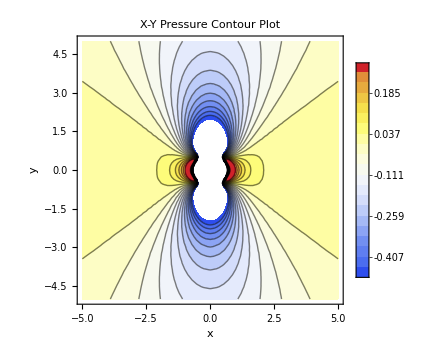

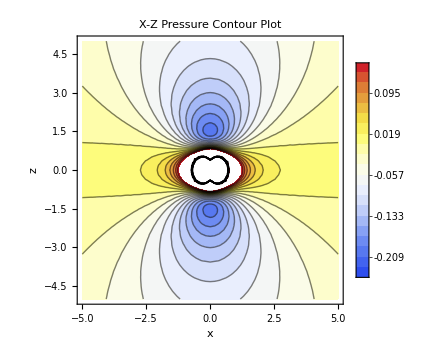

-Graphics-

5/16 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2 (-2/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^6)+16/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^5)-21/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(9/2))+15/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^4)-8/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(7/2))+4/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(5/2)))+1/48 Sin[θ]^2 Sin[ϕ]^2 (-6/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^5)+45/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(7/2))-75/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^3)-8/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(5/2))-20/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(3/2)))+1/48 Cos[ϕ]^2 Sin[θ]^2 (-6/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^5)+45/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(7/2))-75/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^3)+32/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(5/2))+20/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(3/2)))+1/48 (-9/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^(5/2))+25/((Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)^2)-20/(√(Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)))

```mathematica
pPeery1=pPeery/.z->0;
pPeery2=pPeery/.y->0;
pPeery3=pPeery/.x->0;
Scode1=ContourPlot[pPeery1,{x,-5,5},{y,-5,5},Contours->20,ContourShading->True,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,Frame->True,FrameLabel->{"x","y"},Axes->False,PlotLabel->Style["X-Y Pressure Contour Plot",14,Bold],ImageSize->Medium,PlotLegends->Automatic]
Scode2=ContourPlot[pPeery2,{x,-5,5},{z,-5,5},Contours->20,ContourShading->True,ColorFunction->"TemperatureMap",(*Smooth,perceptual color scale*)ColorFunctionScaling->True,Frame->True,FrameLabel->{"x","z"},Axes->False,PlotLabel->Style["X-Z Pressure Contour Plot",14,Bold],ImageSize->Medium,PlotLegends->Automatic]
Scode3=ContourPlot[pPeery3,{y,-5,5},{z,-5,5},Contours->20,ContourShading->True,ColorFunction->"TemperatureMap",(*Smooth,perceptual color scale*)ColorFunctionScaling->True,Frame->True,FrameLabel->{"y","z"},Axes->False,PlotLabel->Style["Y-Z Pressure Contour Plot",14,Bold],ImageSize->Medium,PlotLegends->Automatic]
psphPeery=pPeery/.{x->r Sin[θ]Cos[ϕ],y->r Sin[θ]Sin[ϕ],z->r Cos[θ],Assumptions-> {Im[r]==0,Re[r]>0}}/.(x^2+y^2+z^2)->1
```

```mathematica
e=(Γ+Γ')/2;
o=(Γ-Γ')/2;
pcodenew=(-1/(2 r^10)-55/(18 r^7)-25/(4 r^6)-203/(40 r^5)) (e.X).(e.X)+5/144 (-18/r^12+144/r^10+154/r^9+135/r^8-72/r^7+36/r^5) Total[Total[Table[e[[i]]  XX[[i]],{i,1,3}]]]+(-3/(50 r^5)-5/(3 r^3)) (e.X).(o.X)+1/720 (220/r^5+750/r^4+1458/r^3+2625/r-120 r^2)Total[Total[Table[e[[i]]  e[[i]],{i,1,3}]]]+1/12 (-7/r-2 r^2) Total[Total[Table[o[[i]]  o[[i]],{i,1,3}]]];
```

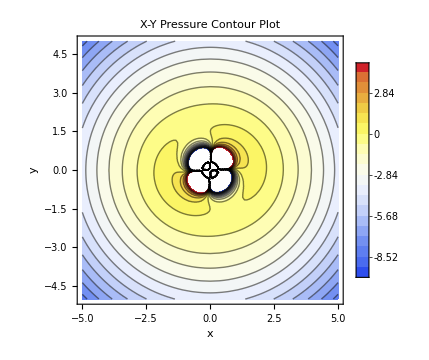

-Graphics-

-Graphics-

```mathematica
pcodenew1=pcodenew/.z->0;
pcodenew2=pcodenew/.y->0;
pcodenew3=pcodenew/.x->0;
Scodenew1=ContourPlot[pcodenew1,{x,-5,5},{y,-5,5},Contours->20,ContourShading->True,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,Frame->True,FrameLabel->{"x","y"},Axes->False,PlotLabel->Style["X-Y Pressure Contour Plot",14,Bold],ImageSize->Medium,PlotLegends->Automatic]
Scodenew2=ContourPlot[pcodenew2,{x,-5,5},{z,-5,5},Contours->20,ContourShading->True,ColorFunction->"TemperatureMap",(*Smooth,perceptual color scale*)ColorFunctionScaling->True,Frame->True,FrameLabel->{"x","z"},Axes->False,PlotLabel->Style["X-Z Pressure Contour Plot",14,Bold],ImageSize->Medium,PlotLegends->Automatic]
Scodenew3=ContourPlot[pcodenew3,{y,-5,5},{z,-5,5},Contours->20,ContourShading->True,ColorFunction->"TemperatureMap",(*Smooth,perceptual color scale*)ColorFunctionScaling->True,Frame->True,FrameLabel->{"y","z"},Axes->False,PlotLabel->Style["Y-Z Pressure Contour Plot",14,Bold],ImageSize->Medium,PlotLegends->Automatic]
```